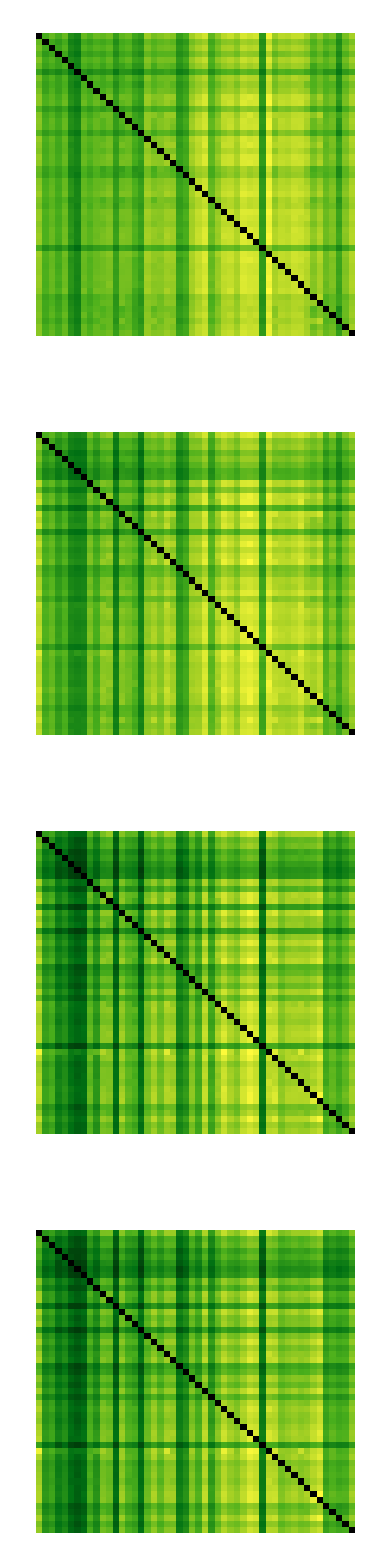

```mathematica
basedir="/Users/olav/Desktop/Doktorarbeit/Imaging/transferentropy/20090820/output/";
SetDirectory@basedir;

TEmatrix=<<("TE_xpart"<>ToString@#<>".mx")&/@Range[4];

GraphicsColumn[ArrayPlot[#,ColorFunction->"AvocadoColors",ImageSize->Medium]&/@TEmatrix]
```

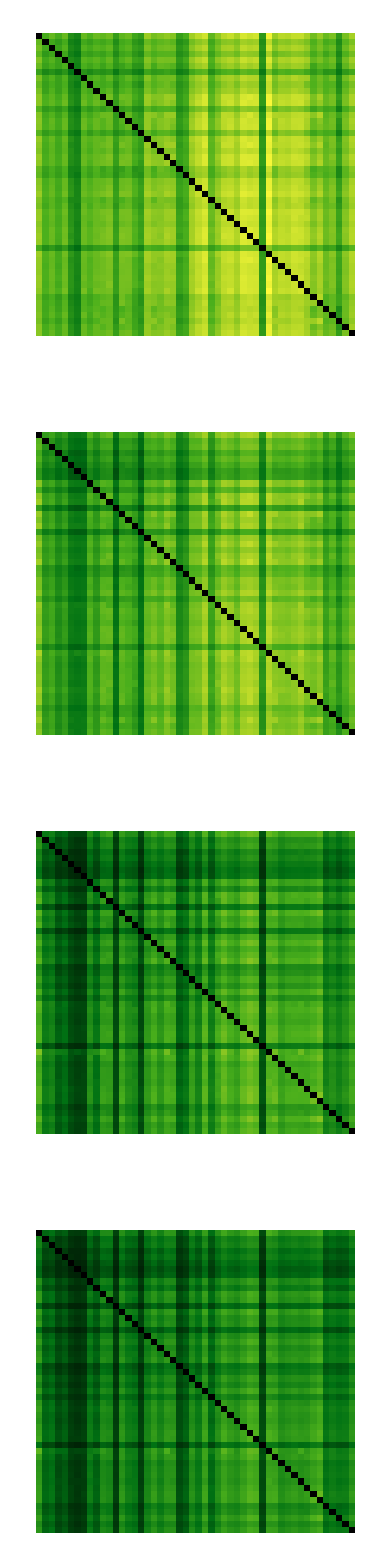

```mathematica
GraphicsColumn[ArrayPlot[#/(Max@Flatten@TEmatrix),ColorFunction->"AvocadoColors",ColorFunctionScaling->False,ImageSize->Medium]&/@TEmatrix]
```

0.960043

0.

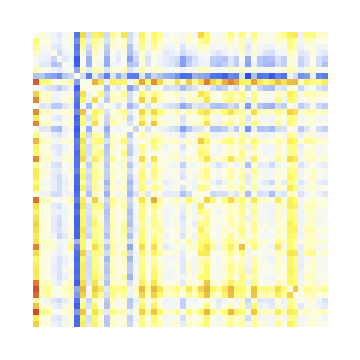

```mathematica
diffmatrix=TEmatrix⟦2⟧/(Mean@Flatten@TEmatrix⟦2⟧)-TEmatrix⟦1⟧/(Mean@Flatten@TEmatrix⟦1⟧);
diffmatrix/= 2 Max@Abs@{Max@diffmatrix,Min@diffmatrix};
diffmatrix+=0.5;
Max@diffmatrix
Min@diffmatrix
ArrayPlot[diffmatrix,ColorFunction->"TemperatureMap",ColorFunctionScaling->False,ImageSize->Medium]
```